## Pics

{-2 (1-x1)-40 x1 (-x1^2+x2),20 (-x1^2+x2)}

{{2+80 x1^2-40 (-x1^2+x2),-40 x1},{-40 x1,20}}

11-2 x1+20 x2+1/2 (-38 x1^2+20 x2^2)

11-2 x1+20 x2

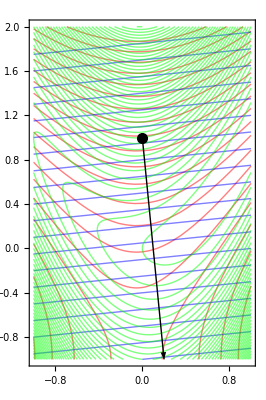

```mathematica
f[{x1_,x2_}]:= 10(x2-x1^2)^2 + (1 - x1)^2 
df[{x1_,x2_}]=D[ f[{x1,x2}],{{x1,x2}}]
ddf[{x1_,x2_}]=D[ f[{x1,x2}],{{x1,x2},2}]
y={0,1}; 
m[{x1_,x2_}]= f[y]+df[y].{x1,x2} + 1/2 {x1,x2}.ddf[y].{x1,x2}
mm[{x1_,x2_}]= f[y]+df[y].{x1,x2} 
Show[
ContourPlot[ m[{x1,x2}], {x1,-1,1},{x2,-1,2},
Contours->20,
ContourStyle->Red,
ContourShading->False],
ContourPlot[ mm[{x1,x2}], {x1,-1,1},{x2,-1,2},
Contours->20,
ContourStyle->Blue,
ContourShading->False],
ContourPlot[ f[{x1,x2}], {x1,-1,1},{x2,-1,2},
Contours->43,
ContourStyle->Green,
ContourShading->False],
Epilog->{PointSize[0.02],Point[y], Arrow[{y, y- 0.1df[y]}]},
AspectRatio->Automatic
]
```

A matrix is S if A=Aᵀ  A S matrix is SSPD if it is S and xᵀAx ≥0 for all x.   A is SPD if xᵀAx >0 for all x≠0.

```mathematica
m=12;
B= RandomReal[{-1,1},{m,m}]; 
A=B+Bᵀ;
{lambdas,Vs}=Eigensystem[A];
Chop[Vsᵀ.Vs];
Chop[Vs.A.Vsᵀ]
lambdas
```

{{5.45116,0,0,0,0,0,0,0,0,0,0,0},{0,-4.91195,0,0,0,0,0,0,0,0,0,0},{0,0,-3.38736,0,0,0,0,0,0,0,0,0},{0,0,0,3.10556,0,0,0,0,0,0,0,0},{0,0,0,0,2.81725,0,0,0,0,0,0,0},{0,0,0,0,0,-2.48337,0,0,0,0,0,0},{0,0,0,0,0,0,2.2388,0,0,0,0,0},{0,0,0,0,0,0,0,1.64961,0,0,0,0},{0,0,0,0,0,0,0,0,-1.49657,0,0,0},{0,0,0,0,0,0,0,0,0,0.969175,0,0},{0,0,0,0,0,0,0,0,0,0,-0.59797,0},{0,0,0,0,0,0,0,0,0,0,0,-0.209243}}

{5.45116,-4.91195,-3.38736,3.10556,2.81725,-2.48337,2.2388,1.64961,-1.49657,0.969175,-0.59797,-0.209243}

## Conjugate Gradients

### Linear Conjugate Gradients (non-blocked)

See chapter 5 of Nocedal and Wright.  Pay particular attention to the preliminary conjugate directions material.  The standard version uses/creates single directions p_i one at a time.  The standard initial development is for a convex quadratic cost function i.e. A is SPD
	f(x) = 0.5 x.A.x+g.x
Rewrite the conjugate gradient algorithm as  
	α_(k+1)=argmin(f(x_k+p_k α))
which has an explicit formula and update according to. 
	x_(k+1)=x_k+α_(k+1)p_k
update for  gradient g_(k+1)=∇f(x_k)=A.x_k+g  update for p_(k+1) is essentially just orthogonalization against p_k
	p_(k+1)=∇f(x_(k+1))=A.x_(k+1)+g
	p_(k+1)=p_(k+1)-(p_(k+1).p_k)p_k
	p_(k+1)=p_(k+1)/||p_(k+1)||

### Linear Conjugate Gradients (block version)

Again for a convex quadratic cost function i.e. A is SPD
	f(x) = 0.5 x.A.x+g.x
but now using conjugate blocks P_i
	(a⃗)_(k+1)=argmin(f(x_k+P_k α⃗))
which again has an explicit formula and update
	x_(k+1)=x_k+P_k (α⃗)_(k+1)
and we can update P_(k+1) as follows
	P_(k+1)=A.P_k+g
	P_(k+1)=P_(k+1)-(P_(k+1).P_k)P_k
	P_(k+1)=orth(P_(k+1))

### Nonlinear Conjugate Gradients

Again chapter 5 of Nocedal and Wright.  For a nonlinear function f you typically do a line search 
	α_(k+1)≈argmin f(x_k+α_k p_k)
with a variety of tests to make sure your α is OK.  Then update similarly to before.   Not common but you could replace the  line search with a “trust region” this means replace f with a quadratic model function 
	m_k(p)=0.5 p.B_k.p +g_k.p+f(x_k)≈f(x_k+p)
in the minimization and take the analytically determined 
	a_(k+1)=argmin_(|α |≤ Δ_k)(m_k(p_k α))
The trust region radius Δ_k prevents large steps and is updated according to a simple rule. Now we need to know how to update lots of bits: B_k and g_k and Δ_k

### Nonlinear Conjugate Gradients (Block and Simplest)

Compute g_k=∇f(x_k) and P_(k+1)=∇^2 f(x_k).P_k  using forward-mode AD tools simultaneously. Define
	B_(k+1)=P_k ᵀ.∇^2 f(x_k).P_k
and minimize
	m_k(α⃗)=0.5 α⃗.B_k.α_k+g_k.P_k α⃗
over a trust region i.e. 
	(α⃗)_(k+1)=argmin_(|α⃗ |≤  Δ_k)(m_k(α⃗))
Step 
	x_(k+1)=x_k+P_k.α_(k+1)
and update 
	P_(k+1)=P_(k+1)-(P_k.P_(k+1)).P_k
	P_(k+1)=orth(P_(k+1))
Update the trust region radius Δ_k.

## Conjugate Gradients Implementation

### STD CG (no block)

The code I worked from is solving A.x=b rather than minimizing  0.5 x.A.x+g  there is a minus sign

```mathematica
CGStep[A_][{x_,r_,p_}]:= Module[{α,β, Ap=A.p, xNew,rNew,pNew},
α=r.r/p.Ap;
xNew = x+ α p;
rNew = r - α Ap;
β = rNew.rNew/r.r;
pNew = rNew + β p;
{xNew,rNew,pNew}]
```

```mathematica
Clear[f,g]
m=12; A=RandomReal[{-1,1},{m,m}];A=A.Aᵀ; g = RandomReal[{-1,1},m];
f[x_]:= 0.5 x.A.x+ g.x; Df[x_]:=A.x+g;
xLinSol = -LinearSolve[A,g];

MaxIter = m;
{x,r,p}=Nest[CGStep[A],{0*g,-g,-g},MaxIter];
x-xLinSol
```

{-7.08655×10^-11,-1.18177×10^-10,8.87761×10^-11,2.84901×10^-11,1.4592×10^-11,5.62034×10^-12,-1.50333×10^-10,3.20393×10^-11,7.21925×10^-11,3.60646×10^-11,1.05405×10^-10,8.46576×10^-11}

### AD CG (no block)

I am going to rework this to use derivatives: g(x) is the gradient function and H(x) is the Hessian function.  Hopefully this will look less cryptic than the “algorithm” above.  All of the following are the same (up to floating point stuff) as the version above for convex quadratic function.  They are not the same if you relax this assumption.   I implemented the four variants on the wiki page “nonlinear conjugate gradient method”.   The notations do not match up exactly!
FR	Fletcher Reeves
PR     Polak-Ribiere
HS	Hestenes Stiefel
DY    Dai-Yuan

```mathematica
Clear[βCG,ΔxOld,ΔxNew,sOld]
βCG["FR",{ΔxOld_,ΔxNew_,sOld_}]:= ΔxNew.ΔxNew/(ΔxOld.ΔxOld)
βCG["PR",{ΔxOld_,ΔxNew_,sOld_}]:= ΔxNew.(ΔxNew-ΔxOld)/(ΔxOld.ΔxOld)
βCG["HS",{ΔxOld_,ΔxNew_,sOld_}]:= ΔxNew.(ΔxNew-ΔxOld)/(-sOld.(ΔxNew-ΔxOld))
βCG["DY",{ΔxOld_,ΔxNew_,sOld_}]:= ΔxNew.ΔxNew/(-sOld.(ΔxNew-ΔxOld))
```

```mathematica
CGStepAD[{f_,g_,H_}][{x_,p_}]:= Module[
{α,β,SD, DGrad, xNew,pNew},
 SD=-g[x];               (* Steepest Descent vector *)
Alg ="FR";
β =βCG[Alg, ΔxOld,ΔxNew,sOld];
XXXXX;
DGrad = H[x].p ;    (* vector *)
(* Optimum step for scalar quadratic model *)
α=-(grad.p)/(DGrad.p);
xNew = x+ α p;
(* Perp and Orthogonalize new direction *)
pNew=DGrad - (DGrad.p)p;
pNew = Normalize[pNew];
{xNew,pNew}]
```

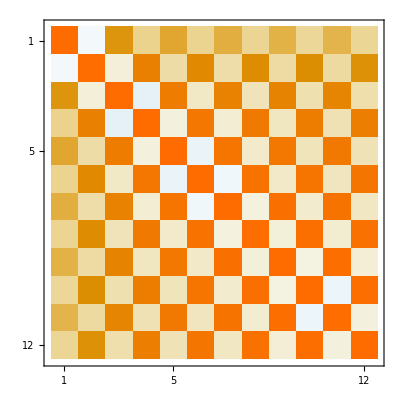

```mathematica
Clear[f,g,H]
m=12; A=RandomReal[{-1,1},{m,m}];A=A.Aᵀ; b = RandomReal[{-1,1},m];
f[x_]:= 0.5 x.A.x+ b.x; g[x_]:=A.x+b; H[x_] :=A
xLinSol = -LinearSolve[A,b];

MaxIter = m;
x0 = 0*b;
Data = NestList[CGStepAD[{f,g,H}],{x0,Normalize[g[x0]]},MaxIter];
ps= Data⟦All,2⟧;
MatrixPlot[Table[ ps⟦i⟧.ps⟦j⟧,{i,MaxIter},{j,MaxIter}]]
```

```mathematica
xLinSol
```

{12.4485,8.26971,-26.2992,-13.3406,3.19191,-19.9601,-4.21062,20.4347,-3.55527,-5.43343,33.7131,-20.3236}

## GEV trust region solver

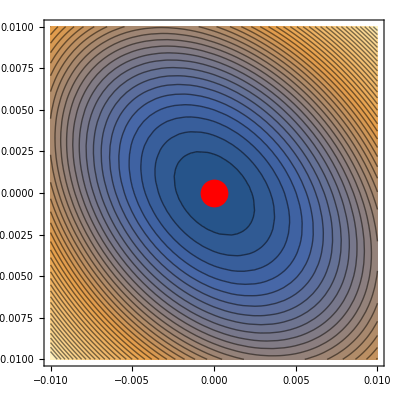

```mathematica
n=4;
{G,B}=RandomReal[{-1,1},{2,n,n}]; 
{G,B}={G+Gᵀ,B.Bᵀ};
B=IdentityMatrix[n];
g=RandomReal[{-1,1},n];
f[p_]:= 0.5 p.G.p + g.p
R=0.2;
{M1,M2}=Map[ArrayFlatten,{({{-B, G}, {G, -KroneckerProduct[g,g]/R^2}}),({{0, B}, {B, 0}})}];
{λs,Vs}=Sort[Chop[Eigensystem[ { M1,M2}]]ᵀ,Re[#1⟦1⟧]≤Re[#2⟦1⟧]&]ᵀ;
{y1,y2}=Partition[Vs⟦1⟧,n];
p = - (R^2/g.y2 )y1;
{u1,u2}=Orthogonalize[RandomReal[{-1,1},{2,n}]];
pStar[{α1_,α2_}]:= (R(p+α1 u1 + α2 u2))/(√((p+α1 u1+α2 u2).B.(p+α1 u1+α2 u2)))
ContourPlot[f[pStar[{α1,α2}]], {α1,-ϵ,ϵ},{α2,-ϵ,ϵ},
Epilog->{PointSize[0.05],Red,Point[{0,0}]},
Contours->40]
```

```mathematica
Chop[Eigensystem[ { M1,M2}]]
```

{{-8.19605,6.56215,-2.26052+1.26568 ⅈ,-2.26052-1.26568 ⅈ,1.39423+0.236178 ⅈ,1.39423-0.236178 ⅈ,0.581379+0.667805 ⅈ,0.581379-0.667805 ⅈ},{{-0.760004,0.395923,0.487111,-0.0385051,-0.124672,0.0627825,0.0794145,0.0329827},{0.639309,-0.480312,-0.378969,0.438799,-0.08541,0.0872021,0.0466945,-0.0856864},{0.4598-0.0362068 ⅈ,-0.16244-0.0738915 ⅈ,-0.335897+0.0909085 ⅈ,-0.0434759-0.642511 ⅈ,-0.0818811-0.00882593 ⅈ,0.157997-0.00373969 ⅈ,-0.0267962+0.00947072 ⅈ,0.418132-0.110558 ⅈ},{0.4598+0.0362068 ⅈ,-0.16244+0.0738915 ⅈ,-0.335897-0.0909085 ⅈ,-0.0434759+0.642511 ⅈ,-0.0818811+0.00882593 ⅈ,0.157997+0.00373969 ⅈ,-0.0267962-0.00947072 ⅈ,0.418132+0.110558 ⅈ},{0.057324+0.186378 ⅈ,-0.178383+0.0888378 ⅈ,0.0112229+0.0836265 ⅈ,0.122735+0.037612 ⅈ,-0.603705-0.111589 ⅈ,-0.440775-0.113339 ⅈ,-0.557307-0.0617312 ⅈ,-0.0148451+0.00227182 ⅈ},{0.057324-0.186378 ⅈ,-0.178383-0.0888378 ⅈ,0.0112229-0.0836265 ⅈ,0.122735-0.037612 ⅈ,-0.603705+0.111589 ⅈ,-0.440775+0.113339 ⅈ,-0.557307+0.0617312 ⅈ,-0.0148451-0.00227182 ⅈ},{-0.235839-0.251866 ⅈ,0.266075-0.219491 ⅈ,-0.0927717+0.354858 ⅈ,-0.313519-0.0903153 ⅈ,-0.00788149-0.0811804 ⅈ,0.396754+0.209371 ⅈ,-0.396799-0.388619 ⅈ,-0.0470556-0.0489806 ⅈ},{-0.235839+0.251866 ⅈ,0.266075+0.219491 ⅈ,-0.0927717-0.354858 ⅈ,-0.313519+0.0903153 ⅈ,-0.00788149+0.0811804 ⅈ,0.396754-0.209371 ⅈ,-0.396799+0.388619 ⅈ,-0.0470556+0.0489806 ⅈ}}}

```mathematica
MatrixForm[M2.M1]
```

(-0.553739 | 0.888094 | 1.22554 | 1.20356 | -24.733 | 14.3487 | 15.583 | -9.57917
0.888094 | 0.674935 | -0.0859853 | -1.31797 | 14.3487 | -8.32424 | -9.04037 | 5.55727
1.22554 | -0.0859853 | 0.099241 | -0.408285 | 15.583 | -9.04037 | -9.8181 | 6.03535
1.20356 | -1.31797 | -0.408285 | -1.3223 | -9.57917 | 5.55727 | 6.03535 | -3.71003
-1. | 0. | 0. | 0. | -0.553739 | 0.888094 | 1.22554 | 1.20356
0. | -1. | 0. | 0. | 0.888094 | 0.674935 | -0.0859853 | -1.31797
0. | 0. | -1. | 0. | 1.22554 | -0.0859853 | 0.099241 | -0.408285
0. | 0. | 0. | -1. | 1.20356 | -1.31797 | -0.408285 | -1.3223)

```mathematica
λs
```

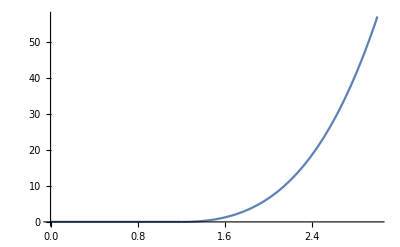

```mathematica
R=1.2;
Plot[ Max[0,x^2-R^2 ]^2,{x, 0, 3}]
```

# Break

```mathematica
n=2234;
Q=Orthogonalize[RandomReal[{-1,1},{n,n}]];
A=Q.DiagonalMatrix[Join[{100,-1.2},RandomReal[{-1,1},n-2]]].Qᵀ;
ϵ=0.00001;
{
Timing[{{λ1},{v1}}=Eigensystem[-A,1,Method->{Automatic,"Criteria"->"RealPart"}];λ1],
v0=v+ ϵ RandomReal[{-1,1},n];
Timing[Eigensystem[-A,1,
Method->{"Arnoldi","Criteria"->"RealPart","BasisSize"->8,"StartingVector"->v1}]⟦1⟧]
}
```

{{5.48438,-100.},{0.109375,{1.2}}}

```mathematica
Eigenvalues
```

Eigenvalues

## Block Single Step Arnoldi

I can think about the one sided sample as a single step of a block arnoldi which I then do a restart on.

```mathematica
{n,s}={12,3};
A=RandomReal[{-1,1},{n,n}]; A=A+Aᵀ;
{λs,Vs}=Sort[Eigensystem[A]ᵀ]ᵀ;
λs;
ϵ=0.1;
U0= Orthogonalize[Vs⟦1;;s⟧+ϵ RandomReal[{-1,1},{s,n}]]ᵀ;
Hmm=ArrayFlatten[{{U0,A.U0}}];
{Ritzλ1,RitzVec1}=Eigensystem[U0ᵀ.A.U0];
U1 = U0.RitzVec1;
{Ritzλ2,RitzVec2}=Eigensystem[U1ᵀ.A.U1];
U2 = U1.RitzVec2;

TableForm[
{Ritzλ1,Ritzλ2,λs⟦1;;s⟧}ᵀ,
TableHeadings->{Automatic, {"Ritz1","Ritz1","λ"}}
]
```

| Ritz1 | Ritz1 | λ
1 | -6.30261 | -6.30261 | -6.42818
2 | -4.18236 | -4.18236 | -4.28408
3 | -2.63172 | -2.63172 | -2.74224

```mathematica
Ritzλ1-Ritzλ2
```

{1.15463×10^-14,2.66454×10^-15,0.}

## Lin Alg Updates

I have three updates (one with two distinct implementations) that need to be implemented. I am snagging these from the B unnumbered updates in the last paragraph of section 1 of the LOD paper for DFP (with W = A) and BFGS.
I am implementing the LDLᵀ version of SR1.  I understand that SR1 is (4) with W=|B-A|.  Note, we need to be careful about the SPDness of this! I believe the absolute value fixes the “implementation” but not the underlying issue. I think a little thought about this would understand why SR1 can (and does) make huge corrections at times.

### DFP

```mathematica
Projector["DFP"][{AU_,U_}]:=AU.Inverse[Uᵀ.AU].Uᵀ 
BUpdate["DFP"][{B_,{U_,AU_}}]:= Module[
{P=Projector["DFP"][{AU,U}],Id=IdentityMatrix[Length[B]]},
(* last term rewritten slightly to show dependence only on AU *)
(* displayed Eq from LOD two above section two heading *)
(* This is horribly inefficient *)
(* Julia implementation will be cleaner *)
(Id-P).B.(Id-Pᵀ)+ AU.Inverse[Uᵀ.AU].(AU)ᵀ
]
```

Testing on non-SPD

```mathematica
{n,s}={12,3};
{A,B}=RandomReal[{-1,1},{2,n,n}];{A,B}=Map[ #+#ᵀ&,{A,B}];
U=Orthogonalize[RandomReal[{-1,1},{s,n}]]ᵀ;
AU=A.U;
(* P = Projector["DFP"][{AU,U}];{Dimensions[P],Norm[P.P-P]} *)
BNew=BUpdate["DFP"][{B,{U,A.U}}]; 
{Dimensions[BNew],Norm[BNew.U-AU], Sign[Eigenvalues[BNew]]}
```

{{12,12},1.89818×10^-15,{1,1,-1,-1,-1,1,-1,-1,1,-1,-1,1}}

Testing on SPD.  I now believe that DFP (and of course BFGS) preserve +def automatically in our test case.

```mathematica
{n,s}={233,34};
{QA,QB}=Map[Orthogonalize,RandomReal[{-1,1},{2,n,n}]];
{DA,DB}= Map[DiagonalMatrix[Exp[#]]&,RandomReal[{-12,4},{2,n}]];
{A,B}={QA.DA.QAᵀ,QB.DB.QBᵀ};
U=Orthogonalize[RandomReal[{-1,1},{s,n}]]ᵀ;
AU=A.U;
(* P = Projector["DFP"][{AU,U}];{Dimensions[P],Norm[P.P-P]} *)
BNew=BUpdate["DFP"][{B,{U,A.U}}]; 
{Dimensions[BNew],Norm[BNew.U-AU], Union[Sign[Eigenvalues[BNew]]]}
```

{{233,233},4.21021×10^-13,{1}}

### BFGS

```mathematica
BUpdate["BFGS"][{B_,{U_,AU_}}]:= Module[
{ BU=B.U},
(* last term rewritten slightly to show dependence only on AU *)
(* displayed Eq from LOD directly above section two heading *)
(* This is horribly inefficient *)
(* Julia implementation will be cleaner *)
B-BU.Inverse[Uᵀ.BU].BUᵀ +AU.Inverse[Uᵀ.AU].AUᵀ
]
```

Testing on non-SPD

```mathematica
{n,s}={12,3};
{A,B}=RandomReal[{-1,1},{2,n,n}];{A,B}=Map[ #+#ᵀ&,{A,B}];
U=Orthogonalize[RandomReal[{-1,1},{s,n}]]ᵀ;
AU=A.U;
BNew=BUpdate["BFGS"][{B,{U,A.U}}]; 
{Dimensions[BNew],Norm[BNew.U-AU], Union[Sign[Eigenvalues[BNew]]]}
```

{{12,12},3.39215×10^-15,{-1,1}}

Testing on SPD.  I now believe that BFGS preserves +def automatically in our test case.

```mathematica
{n,s}={233,34};
{QA,QB}=Map[Orthogonalize,RandomReal[{-1,1},{2,n,n}]];
{DA,DB}= Map[DiagonalMatrix[Exp[#]]&,RandomReal[{-12,4},{2,n}]];
{A,B}={QA.DA.QAᵀ,QB.DB.QBᵀ};
U=Orthogonalize[RandomReal[{-1,1},{s,n}]]ᵀ;
AU=A.U;
BNew=BUpdate["BFGS"][{B,{U,A.U}}]; 
{Dimensions[BNew],Norm[BNew.U-AU], Union[Sign[Eigenvalues[BNew]]]}
```

{{233,233},8.94759×10^-14,{1}}

### SR1-LOD, -LOD+,-Eig

The B update in LOD with W=|B-A| should be SR1.  Note I need both B and A for this computation

```mathematica
BUpdate["SR1-LOD+"][{B_,A_,{U_,AU_}}]:= Module[
{W,Vs,λs,P},
{λs,Vs}=Eigensystem[B-A];
(* Remember ᵀ in evecs *)
W=Vsᵀ.DiagonalMatrix[Abs[λs]].Vs;
(* PB equation from LOD just below (4) *)
P=W.U.Inverse[Uᵀ.W.U].Uᵀ;
(* Eq 4 from LOD *)
B+P.(A-B)+(A-B).Pᵀ-P.(A-B).Pᵀ
]

BUpdate["SR1-LOD0"][{B_,A_,{U_,AU_}}]:= Module[
{W,Vs,λs,P},
{λs,Vs}=Eigensystem[B-A];
(* Remember ᵀ in evecs *)
W=Vsᵀ.DiagonalMatrix[Map[Max[0,#]&,λs]].Vs;
(* PB equation from LOD just below (4) *)
P=W.U.Inverse[Uᵀ.W.U].Uᵀ;
(* Eq 4 from LOD *)
B+P.(A-B)+(A-B).Pᵀ-P.(A-B).Pᵀ
]
```

```mathematica
BUpdate["SR1-LOD"][{B_,A_,{U_,AU_}}]:= Module[
{W,P},
(* Remember ᵀ in evecs *)
W=A-B; (* Note this is not suitable as a weight *)
(* PB equation from LOD just below (4) *)
P=W.U.Inverse[Uᵀ.W.U].Uᵀ;
(* Eq 4 from LOD *)
B+P.(A-B)+(A-B).Pᵀ-P.(A-B).Pᵀ
]
```

```mathematica
BUpdate["SR1-SimpleLOD"][{B_,A_,{U_,AU_}}]:= Module[
{W,P},
(* Remember ᵀ in evecs *)
W=A-B; (* Note this is not suitable as a weight *)
(* PB equation from LOD just below (4) *)
P=W.U.Inverse[Uᵀ.W.U].Uᵀ;
(* OK so weight is degenerate with zeros except on the column space of AU-B.U *)
(* Eq 4 from LOD is *)
(* B+P.(A-B)+(A-B).Pᵀ-P.(A-B).Pᵀ *)
(* which simplifies using P.(A-B) = (A-B).Pᵀ = P.(A-B).Pᵀ to *)
B+P.(A-B).Pᵀ
(* *)
]
```

The “algebraic” derivation of Block SR1 follows the single sample variant.  I want 
	(B+L.D.Lᵀ).U=AU
so 
	L.D.Lᵀ.U=(AU-B.U) 
which implies L=(AU-B.U).V	(the column spaces match) so
	(AU-B.U).V.D.Vᵀ.(AU-B.U)ᵀ.U=(AU-B.U)
and multiplying by (AU-B.U)ᵀ and defining G=(AU-B.U)ᵀ.(AU-B.U) which is assumed to be full rank
	 (AU-B.U)ᵀ.(AU-B.U).V.D.Vᵀ.(AU-B.U)ᵀ.U=(AU-B.U)ᵀ.(AU-B.U)
so	
	V.Dia.Vᵀ.(AU-B.U)ᵀ.U=Id
and we can compute V and D as the LDLᵀ decomposition of ((AU-B.U)ᵀ.U)^-1.  The is no LDLᵀ in Mathematica so I am going to do this using an eigenvalue computation.   I can NOT do it with a Cholesky since the internal “correction” matrix (AU-B.U)ᵀ.U while symmetric is almost certainly not positive definite!

```mathematica
BUpdate["SR1-Eig"][{B_,{U_,AU_}}]:= Module[
{Vs,λs},
{λs,Vs}=Eigensystem[(AU-B.U)ᵀ.U];
(* Remember ᵀ in evecs *)
B+ (AU-B.U).Vsᵀ.DiagonalMatrix[1/λs].Vs.(AU-B.U)ᵀ
]
```

Testing on non-SPD. The two updates are NOT identical even though both “work”.

```mathematica
{n,s}={6,3};
{A,B}=RandomReal[{-1,1},{2,n,n}];{A,B}=Map[ #+#ᵀ&,{A,B}];
U=Orthogonalize[RandomReal[{-1,1},{s,n}]]ᵀ;
BNewSR1LOD=BUpdate["SR1-LOD"][{B,A,{U,A.U}}]; 
BNewSR1LODPlus=BUpdate["SR1-LOD+"][{B,A,{U,A.U}}]; 
BNewSR1LOD0=BUpdate["SR1-LOD0"][{B,A,{U,A.U}}]; 
BNewSR1SimpleLOD=BUpdate["SR1-SimpleLOD"][{B,A,{U,A.U}}]; 
BNewSR1Eig=BUpdate["SR1-Eig"][{B,{U,A.U}}]; 
Variants={BNewSR1LOD, BNewSR1LODPlus,BNewSR1LOD0,BNewSR1SimpleLOD,BNewSR1Eig};
TableForm[{Map[Norm[(A-#).U,"Frobenius"]&, Variants],
Map[Norm[A-#,"Frobenius"]&, Variants],
Map[Norm[B-#,"Frobenius"]&, Variants],
Map[Norm[Variants⟦-1⟧-#,"Frobenius"]&, Variants]},
TableHeadings->{{"U-Res","Full-Res","Change","Diff"},{"LOD","LOD+","LOD0","LOD-Sim","SR1Eig"}}]
```

| LOD | LOD+ | LOD0 | LOD-Sim | SR1Eig
U-Res | 2.33399×10^-15 | 7.64761×10^-16 | 9.5059×10^-8 | 5.79349×10^-15 | 1.62575×10^-14
Full-Res | 13.1701 | 1.76329 | 630415. | 13.1701 | 13.1701
Change | 14.3279 | 5.85494 | 630417. | 14.3279 | 14.3279
Diff | 5.16855×10^-14 | 12.5125 | 630418. | 3.93098×10^-14 | 0.

```mathematica
Eigenvalues[PXX]
```

{1.,1.,1.,1.53531×10^-15,3.33067×10^-16,2.7489×10^-16}

Testing on SPD.  SR1 does NOT preserve SPD.  Again not the same update

```mathematica
{n,s}={6,3};
{QA,QB}=Map[Orthogonalize,RandomReal[{-1,1},{2,n,n}]];
{DA,DB}= Map[DiagonalMatrix[Exp[#]]&,RandomReal[{-12,4},{2,n}]];
{A,B}={QA.DA.QAᵀ,QB.DB.QBᵀ};
U=Orthogonalize[RandomReal[{-1,1},{s,n}]]ᵀ;
AU=A.U;
{λs,Vs}=Eigensystem[(AU-B.U)ᵀ.U];
BNewSR1LODPlus=BUpdate["SR1-LOD+"][{B,A,{U,A.U}}]; 
BNewSR1LOD=BUpdate["SR1-LOD"][{B,A,{U,A.U}}]; 
BNewSR1Eig=BUpdate["SR1-Eig"][{B,{U,A.U}}]; 
Map[Norm[#,"Frobenius"]&,{(A-BNewSR1LODPlus).U,(A-BNewSR1LOD).U, (A-BNewSR1Eig).U, 
BNewSR1LOD-BNewSR1Eig, A-BNewSR1LOD,A-BNewSR1Eig}]
```

{√(Abs[-0.162604 (-0.0192112-BUpdate[SR1-LOD+][{1}])-0.00787443 (1)+2+1-0.647653 (1)]^2+Abs[8+1]^2+Abs[1]^2+Abs[1]^2+Abs[1]^2+8+1^2+Abs[1]^2+Abs[1]^2+Abs[7+1]^2+Abs[1]^2),4,19}
 |  |  |  |

## Trust Region Optimization Tools

The plan is to  develop needed  tools in Mathematica and then port to Julia.   I need Julia for the AD tools and the CUTE interface.  I was building only in Julia but that turned out to be a pain.

I am working from 
@book{doi:10.1137/1.9780898719857,
author = {Conn, Andrew R. and Gould, Nicholas I. M. and Toint, Philippe L.},
title = {Trust Region Methods},
publisher = {Society for Industrial and Applied Mathematics},
year = {2000},
doi = {10.1137/1.9780898719857},
address = {},
edition   = {},
URL = {https://epubs.siam.org/doi/abs/10.1137/1.9780898719857},
eprint = {https://epubs.siam.org/doi/pdf/10.1137/1.9780898719857}
}
which I abbreviate TRM.

I am only doing spherical L2 trust regions.

## Notation

α1 is the amount the radius expand while α2 is the amount the radius shrinks in the TR control:  0<α2<1≤α1

η1 is the cut-off from shrinking the TR radius while η2 is the cut-off for growing the TR radius.

Modifications for bad ρ<0 intervention

γ1 is a max control on the modification. TRM recommends γ1=0.0625

γbad is a calculated parameter (17.1.3)

Standard update names f_k=f(x_k), g_k=Df(x_k), B_k≈D^2 f(x_k), H_k≈D^2(f(x_k))^-1 .  B_k and H_k are always symmetric but not SPD.

Model function:  m_k(p)=f_k+p.g_k+0.5 p.B_k.p

I am going to call the radius R rather than Δ.

Not following QN I am going to write the differences as Δx_(k+1)=x_(x+1)-x_k and Δg_(k+1)=g_(x+1)-g_k.  The translation to Nocedal and Wright and the QN literature is s_k=Δx_(k+1) and y_k=Δg_(k+1).  The secant equation the QN terminology is B_(k+1).s_k=y_k.  In my terminology  B_(k+1).Δx_(k+1)=Δg_(k+1).  I like mine better!

## Code

### Trust Region Set-Up and Update

Sections 17.1 and 17.2 contain discussion on parameters etc. for the step up and control.  I want to fix these on easily described standard parameter values.  TRM is the way to go.

#### Trust Region Initialization: From Book

Implementing algorithm 17.2.1 on p787 - boxed.  The algorithm has two iterates: i adjusts the radius the way you would expect; j adjusts the starting point because it is entirely possible that in the search for a good radius a better point has been discovered.  Both are safeguarded  so that it does not become an optimization algorithm instead of an initialization algorithm. 

The convoluted procedure is from Sartenaer.
@article{doi:10.1137/S1064827595286955,
author = {Sartenaer, A.},
title = {Automatic Determination of an Initial Trust Region in Nonlinear Programming},
journal = {SIAM Journal on Scientific Computing},
volume = {18},
number = {6},
pages = {1788-1803},
year = {1997},
doi = {10.1137/S1064827595286955},
URL = { https://doi.org/10.1137/S1064827595286955},
eprint = {https://doi.org/10.1137/S1064827595286955}
}
There is some more recent activity
2014 Open Access article https://www.hindawi.com/journals/jam/2014/610612/
Searching for “cited by” generates a list.

It may well involve quite a few function evaluations!   
Brings up a simple and probably very cool idea: use forward-forward mode AD on the gradient to estimate a radius!

Input:
Initial point x0 and radius R0
function f and g=Df
Parameters:
μ1 and μ2;
γBar1 and γBar2;
jMax and iMax;
Internal Values:
τ  — back of parameter'
σ — Cauchy Step

The structure is confusing the inner “i” loop has not test

```mathematica
Clear[x1,x2,f,g]
(* Define Rosen test Function *)
f[{x1_,x2_}]:= 100.0(x2-x1^2)^2+(1.0-x1)^2
g[{x1_,x2_}]=D[f[{x1,x2}],{{x1,x2}}];
h[{x1_,x2_}]=D[f[{x1,x2}],{{x1,x2},2}];
(* Begin Script for 17.2.1 *)
(* Parametere values are from TRM on p788 *)
{iMax,jMax}={4,1}; j=0;
{γBar1,γBar2,γBar3,γBar4}={0.0625,0.5,2,5};
{{μ1,μ2},θ}={{0.5,0.35},0.25};
{xIn,RIn}={{0.4,0.3},1.2};
{x0,R,RMax}={xIn,RIn, 0};
(* Step 1: *)
(* Not stated: but Subscript[m, 0] is the model function with Subscript[B, 0] "initial" Hessian approx  *)
(* Brings up another obvious thing: surely Subscript[R, 0] and Subscript[B, 0] should be estimated together *)
B0=h[x0];
(* In practice you would not use an exact Hessian *)
(* Initialize tracking of found minimum *)
While[
And[j≤jMax, fMin<f0], 
x0=x0-σ g0; j++;
{f0,g0}={f[x0],g[x0]};
fMin=f0;
(* In practice you would not use an exact Hessian *)
(* Compute the Cauchy point and the function and model values *)
(* Note the minus sign in the gradient! *)
(* This is 17.2.3 *)
Do[
d0=R g0/Norm[g0];
{fNew, mNew}={f[x0-d0],f0-g0.d0 +0.5 d0.B0.d0};
If[fNew<fMin, (fMin=fNew; σ=d0/Norm[g0])];
(* Compute ρ *)
(* This is 17.2.4 *)
ρ = (f0-fNew)/(g0.d0 -0.5 d0.B0.d0);
(* Predicts well if |ρ-1| ≤ μ2 and badly if |ρ-1| > μ1 *)
(* update RMax if decrease is NOT bad *)
If[Abs[ρ-1]≤ μ1, RMax=Max[R,RMax]];
(* Parameters satisfy 0 ≤ μ2 < μ1*)
(* Grow R if good. Shrink if bad. τ is the scale factor *)
(* τ are from a quadratic interpolation bottom of p785 *)
(* τmin < τmax are safeguards *) 
(* θ is how far of 1 we accept *)
gd =g0.d0;
{τ1,τ2}=θ gd{
-1/(θ (f0-gd)+ + (1-θ) (-gd+0.5 d0.B0.d0)-f0),
1/(-θ (f0-gd)+ + (1+θ) (-gd+0.5 d0.B0.d0)-f0)};
{τMin,τMax}=Map[#[{τ1,τ2}]&,{Min,Max}];
(* Decisions are based on the computed τs and a list of parameters γBar satisfying *)
(* 0 ≤ γBar1 ≤ γBar2 ≤ γBar3≤ γBar4. *)
(* Shrink τ is 17.2.11 *)
Shrinkτ=Which[
τMin>1, γBar2,
Or[τMax<γBar1,And[τMin<γBar1,τMax>=1]], γBar1,
And[γBar1<=τ1<1, Not[γBar1<=τ2<1]], τ1,
And[γBar1<=τ2<1, Not[γBar1<=τ1<1]], τ2,
True,τMax];
(* Grow τ is 17.2.12 *)
Growτ=Which[
τMax<1, γBar3,
τMax>γBar4, γBar4,
And[1<=τ1<γBar4, τ2<1], τ1,
And[1<=τ2<γBar4, τ1<1], τ2,
True,τMax];
(* 17.2.13 *)
Lastτ=Which[
τMax<γBar2, γBar2,
τMax>γBar3, γBar3,
True,τMax];
(* Finally an update *)
τ = Which[
Abs[ρ-1]>μ1, Shrinkτ,
Abs[ρ-1]≤μ2, Growτ,
True,Lastτ];
R=R*τ,
{iMax}]];
```

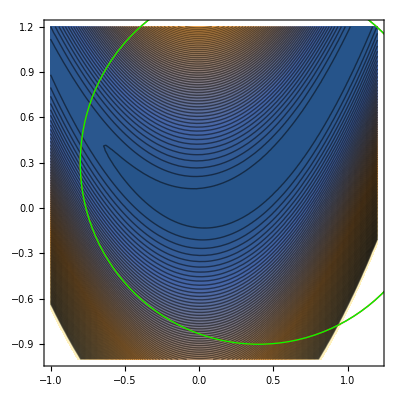

{{0.4,0.3},1.2,0}

```mathematica
ContourPlot[ f[{x1,x2}],{x1,-1,1.2},{x2,-1,1.2},Contours->100,
Epilog->{
{Red,Circle[x0,R]},
 {Green,Circle[xIn,RIn]}
}]
{x0,R,RMax}
```

```mathematica
j=0;
j++
j
```

0

1

```mathematica
Switch
```

Switch

```mathematica
InitializeTrustRegion[{{μ1_,μ2_},{iMax_,jMax_}},{f_,g_}][x0_,R0_]:= Module[
{i=0,j=0, f0=f[x0],RMax = 0,
d0,m0,f0,ρ0},
(* Step 1 from Alg: Max rad UpDate *)

(* Step 2 from Alg *)
(* Step 3 from Alg *)
```

```mathematica
?While
```

#### Trust Region and Hessian Initialization: NOVEL

Clearly you should initialize the trust region and Hessian together.  Clearly you can use AD to get some soirt of decent idea.  Assume I have Df:ℝ^n→ℝ^n as a primitive and an initial point x_0. 
	I can compute a set of "s_1" sampled directional derivatives (specified by an orthogonal  S_1∈ℝ^(n×s_1)) of Df(x_0) which is D2=DDf(x_0).S_1.  This data of course n×s_1! 
	I can also compute sampled mixed second derivatives (specified by orthogonal  matrices S_1∈ℝ^(n×s_`) and S_2∈ℝ^(n×s_2) which is  D3=DDf(x_0).S_1.S_2  This data of course n×s_1×s_2!

Hessian First
The correct thing to do would seem to be to compute the best symmetric matrix consistent with the D2 constraint.  Best could mean smallest in Frobenius norm.  Best could mean lowest L1 norm as a proxy for rank.  It might be possible to do a straight rank s_1 it might be possible to do nearest Kronecker product but that brings up a whole new kettle of fish.

Trust Region Radius
Having picked a B0.  The difference between my model function 
	m_0(p)=f_0+g_0.p+0.5 p.B0.p  and my best guess  
for a cubic fit 
	m_0(p)+1/6 Γ.p.p.p
has relative error  (which looks like ρ  for now)
	(1/6 Γ.p.p.p)/(m_0(p) + 1/6 Γ.p.p.p)
to make progress replace the bottom (maybe) with m_0(p).  There are multiple questions here. 
	γ[p]=(1/6 Γ.p.p.p)/(f_0 + g_0.p + 0.5 p.B.p)
Clearly this generically grows linearly for large p.  I have s directions  ps p_1,…,p_s

#### Trust Region Update

A slightly extended standard update algorithm is recommended in (17.1.4) on p783.  It is implemented below using the TRM notation

```mathematica
UpdateRadius[{{α1_,α2_},{η1_,η2_},γ1_}][R_, {s_,fNew_},{fOld_, gOld_}]
```

### Trust Region Solvers

All the solvers do is take the specification of a model function {f_k,g_k,B_k} and a radius R and return the approximate minimizer for the trust region problem
	s=argmin_(||p||≤R)(f_k+p.g_k+0.5 p.B_k.p)
I have a collection of strategies to implement.

#### Cauchy Point

#### Dogleg

#### Double Dogleg

#### 2D Minimization

#### Iterative n×n Eigenvalue from Secular Equation

#### Non-Iterative 2n×2n Generalized Eigenvalue Problem

#### Hard Case

Both of the eigenvalue problems really require implementing the hard case.  I would like to know if it is really needed.  Part of me feels that a perturbation analysis would show that the hard case did not matter. Specifically it seems to me that sneezing (maybe formally in the sense of re-updating a matrix would avoid the need to do what looks like a structurally unstable special case.  In the n×n algorithm you can miss the hard (or nearly hard) case.  I need to think about how you can miss the hard-case in the larger matrix problem. There is a discussion somewhere about the nearly hard case.

### Hessian up-daters from gradient differences over single steps: Data is 2 vectors each n×1

I write the differences as Δx_(k+1)=x_(x+1)-x_k and Δg_(k+1)=g_(x+1)-g_k.   Averaging the Hessian I can define  OverBar[∇^2 f]_(k+1/2)=∫_(τ=0)^1 ∇^2 f(x_k+τ Δx_(k+1))dτ  which satisfies OverBar[∇^2 f]_(k+1/2).Δx_(k+1)=Δg_(k+1).   We require the secant condition	
	 B_(k+1).Δx_(k+1)=Δg_(k+1)
to hold for our Hessian updates. A second interpretation from 1D calc is that  ∇^2 f(x_k+τ Δx_(k+1)).Δx_(k+1)=Δg_(k+1) for some 0≤τ≤1.

The SR1 is update is fully determined by the minimal algebraic form. It does not always exist.  It does not preserve positivity.  It can have very large updates.  
	The DFP update for B_(k+1)≈∇^2 f(x_(k+1)) is defined by minimization principle
		B_(k+1)=argmin_B||W^(1/2).(B-B_k).W^(1/2)(||)_F  with B=Bᵀ and B.Δx_(k+1)=Δg_(k+1)
where the weight W^-1=OverBar[∇^2 f]_(k+1/2)  . Note the minimizer is the same for any SPD W satisfying W.Δg_(k+1)=Δx_(k+1).
	The BFGS update for H_(k+1)≈(∇^2 f(x_(k+1)))^-1 is defined by minimization principle
		H_(k+1)=argmin_H||W^(1/2).(H-H_k).W^(1/2)(||)_F  with H=Hᵀ and H.Δg_(k+1)=Δx_(k+1)
where the weight W=OverBar[∇^2 f]_(k+1/2)  . Note the minimizer is the same for any SPD W satisfying W.Δx_(k+1)=Δg_(k+1).  Note BFGS and DFP can enforce positivity by only making updates consistent with positivity.  In particular, minimizing a strictly convex quadratic the updates are SPD. 
	The update formulas are translated (s_k=Δx_(k+1) and y_k=Δg_(k+1)) from Nocedal and Wright.  I did the B and H versions for all of them.

#### SR1

```mathematica
SR1UpdateB[{B_,{Δx_,Δg_}}]:=Module[{ΔgMinusBΔx = Δg-B.Δx },
 B+KroneckerProduct[ΔgMinusBΔx,ΔgMinusBΔx]/(ΔgMinusBΔx.Δx)
]
SR1UpdateH[{H_,{Δx_,Δg_}}]:= Module[{ΔxMinusHΔg = Δx-H.Δg },
 H+KroneckerProduct[ΔxMinusHΔg,ΔxMinusHΔg]/(ΔxMinusHΔg.Δg)
]
```

#### BFGS

```mathematica
BFGSUpdateB[{B_,{Δx_,Δg_}}]:=Module[{BΔx=B.Δx,ρ=1/(Δx.Δg)},
(* N&W 6.19 p140 *)
 B-KroneckerProduct[BΔx,BΔx]/(Δx.BΔx)+ρ KroneckerProduct[Δg,Δg]
]
BFGSUpdateH[{H_,{Δx_,Δg_}}]:= Module[
{Id=IdentityMatrix[Length[H]],ρ=1/(Δx.Δg)},
(Id- ρ KroneckerProduct[Δx,Δg]).H.(Id- ρ KroneckerProduct[Δg,Δx])+ ρ KroneckerProduct[Δx,Δx]
]
```

#### DFP

```mathematica
DFPUpdateB[{B_,{Δx_,Δg_}}]:=  Module[
{Id=IdentityMatrix[Length[B]],ρ=1/(Δx.Δg)},
(* N&W 6.17 p140 *)
(Id- ρ KroneckerProduct[Δg,Δx]).B.(Id- ρ KroneckerProduct[Δx,Δg])+ ρ KroneckerProduct[Δg,Δg]
]
DFPUpdateH[{H_,{Δx_,Δg_}}]:= Module[{HΔg=H.Δg,ρ=1/(Δx.Δg)},
(* N&W 6.15 p139 *)
 H-KroneckerProduct[HΔg,HΔg]/(Δg.HΔg)+ρ KroneckerProduct[Δx,Δx]
]
```

#### Testing: SPD

```mathematica
n=6;
(* Build test problems *)
{A,B,H}=RandomReal[{-1,1},{3,n,n}]; {A,B,H}=Map[#.#ᵀ&,{A,B,H}];
InvA=Inverse[A];
Δx=RandomReal[{-1,1},n];Δg=A.Δx;
(* Apply B and H updates *)
NewBs=Map[ #[{B,{Δx,Δg}}]&,{SR1UpdateB,BFGSUpdateB,DFPUpdateB}];
NewHs=Map[ #[{H,{Δx,Δg}}]&,{SR1UpdateH,BFGSUpdateH,DFPUpdateH}];
(* Verify secant equations *)
Max[{Map[ Norm[Δg-#.Δx]&,NewBs],
Map[ Norm[Δx-#.Δg]&,NewHs]}]
(* Verify Sym *)
Max[{Map[ Norm[#-#ᵀ]&,NewBs],
Map[ Norm[#-#ᵀ]&,NewHs]}]
(* verify SPD *)
(* First column is SR1 *)
TableForm[{Map[Union[Sign[Eigenvalues[#]]]&,NewBs],
Map[Union[Sign[Eigenvalues[#]]]&,NewHs]},
TableHeadings->{{"Bs","Hs"},{"SR1", "BFGS","DFP"}}]
(* The B Updates satisfy the B constraints *)
(* The H Updates satisfy the H constraints *)
(* Check the minization WRT perturbation by the other matrices *)
{BFGSw,DFPw}={MatrixPower[A,1/2],MatrixPower[InvA,1/2]};
TabView[{
"B"->TabView[{"SR1B"->ContourPlot[ 
Norm[ DFPw.({1-ϵ2-ϵ3,ϵ2,ϵ3}.NewBs-B).DFPw,"Frobenius"],
{ϵ2,-0.5,0.5},{ϵ3,-1,1},
Contours->10,
Epilog->{Red, PointSize[0.05],Point[{0,0}]},
FrameLabel->{"ϵ2","ϵ3"}],
"BFGSB"->ContourPlot[
Norm[ DFPw.({ϵ1,1-ϵ1-ϵ3,ϵ3}.NewBs-B).DFPw,"Frobenius"],
{ϵ1,-0.5,0.5},{ϵ3,-1,1},
Contours->10,
Epilog->{Red, PointSize[0.05],Point[{0,0}]},
FrameLabel->{"ϵ1","ϵ3"}],
"DFPB"->ContourPlot[ 
Norm[ DFPw.({ϵ1,ϵ2,1-ϵ1-ϵ2}.NewBs-B).DFPw,"Frobenius"],
{ϵ1,-0.5,0.5},{ϵ2,-1,1},
Contours->10,
Epilog->{Red, PointSize[0.05],Point[{0,0}]},
FrameLabel->{"ϵ1","ϵ2"}]},3],
"H"->TabView[{"SR1H"->ContourPlot[ 
Norm[ BFGSw.({1-ϵ2-ϵ3,ϵ2,ϵ3}.NewHs-H).BFGSw,"Frobenius"],
{ϵ2,-0.5,0.5},{ϵ3,-1,1},
Contours->10,
Epilog->{Red, PointSize[0.05],Point[{0,0}]},
FrameLabel->{"ϵ2","ϵ3"}],
"BFGSH"->ContourPlot[
Norm[ BFGSw.({ϵ1,1-ϵ1-ϵ3,ϵ3}.NewHs-H).BFGSw,"Frobenius"],
{ϵ1,-0.5,0.5},{ϵ3,-1,1},
Contours->10,
Epilog->{Red, PointSize[0.05],Point[{0,0}]},
FrameLabel->{"ϵ1","ϵ3"}],
"DFPH"->ContourPlot[ 
Norm[ BFGSw.({ϵ1,ϵ2,1-ϵ1-ϵ2}.NewHs-H).BFGSw,"Frobenius"],
{ϵ1,-0.5,0.5},{ϵ2,-1,1},
Contours->10,
Epilog->{Red, PointSize[0.05],Point[{0,0}]},
FrameLabel->{"ϵ1","ϵ2"}]},2]}]
```

1.27555×10^-15

1.16989×10^-15

| SR1 | BFGS | DFP
Bs | -1
1 | 1 | 1
Hs | -1
1 | 1 | 1

12

#### Testing: ±

```mathematica
n=6;
(* Build test problems *)
{A,B,H}=RandomReal[{-1,1},{3,n,n}]; {A,B,H}=Map[#+#ᵀ&,{A,B,H}];
InvA=Inverse[A];
Δx=RandomReal[{-1,1},n];Δg=A.Δx;
(* Apply B and H updates *)
NewBs=Map[ #[{B,{Δx,Δg}}]&,{SR1UpdateB,BFGSUpdateB,DFPUpdateB}];
NewHs=Map[ #[{H,{Δx,Δg}}]&,{SR1UpdateH,BFGSUpdateH,DFPUpdateH}];
(* Verify secant equations *)
Max[{Map[ Norm[Δg-#.Δx]&,NewBs],
Map[ Norm[Δx-#.Δg]&,NewHs]}]
(* Verify Sym *)
Max[{Map[ Norm[#-#ᵀ]&,NewBs],
Map[ Norm[#-#ᵀ]&,NewHs]}]
(* verify SPD *)
(* First column is SR1 *)
TableForm[{Map[Union[Sign[Eigenvalues[#]]]&,NewBs],
Map[Union[Sign[Eigenvalues[#]]]&,NewHs]},
TableHeadings->{{"Bs","Hs"},{"SR1", "BFGS","DFP"}}]
(* The B Updates satisfy the B constraints *)
(* The H Updates satisfy the H constraints *)
```

3.20983×10^-14

2.60247×10^-14

| SR1 | BFGS | DFP
Bs | -1
1 | -1
1 | -1
1
Hs | -1
1 | -1
1 | -1
1

### Hessian Up-daters using "s" one-sided samples n×s. Philosophically identical to amortizing "s" gradient differences. Secant System: B→B+α U.Uᵀ where B.X=G where U and X are n×s

The SR1 is update is fully determined by the minimal algebraic form but can have very large updates.  
As before, the DFP update for B_(k+1)≈∇^2 f(x_(k+1)) is defined by minimization principle
		B_(k+1)=argmin_B||W^(1/2).(B-B_old).W^(1/2)(||)_F  with B=Bᵀ and B.X=G
where the weight W^-1=OverBar[∇^2 f]_(k+1/2)  . Note the minimizer is the same for any SPD W satisfying W.G=X.
	The BFGS update for H_(k+1)≈(∇^2 f(x_(k+1)))^-1 is defined by minimization principle
		H_(k+1)=argmin_H||W^(1/2).(H-H_k).W^(1/2)(||)_F  with H=Hᵀ and H.G=X
where the weight W=OverBar[∇^2 f]_(k+1/2)  . Note the minimizer is the same for any SPD W satisfying W.Δx_(k+1)=Δg_(k+1).  Note BFGS and DFP can enforce positivity by only making updates consistent with positivity.  In particular, minimizing a strictly convex quadratic the updates are SPD.   I can assume that the input directions U satisfy Uᵀ.U=Id_s in which case the constraints are consistent.  I did the B and H versions for all of them.

#### SR1: B Form

The argument is pretty simple.  I need to solve the n×s equations
	(B+U.D.Uᵀ).X=G
for the n×s matrix U and s×s diagonal matrix D. The argument follows the scalar s=1 case pretty closely.  So
	U.D.Uᵀ.X=G-B.X
which means that U is a combination of the columns of the mismatch i.e. U=(G-B.X).V which we can plug in to get
	(G-B.X).V.D.Vᵀ.(G-B.X)ᵀ.X=G-B.X
which we can multiply by the mismatch transposed (G-B.X)ᵀ to get 
	Γ.V.D.Vᵀ.(G-B.X)ᵀ.X=Γ
where Γ=(G-B.X)ᵀ.(G-B.X) is s×s SSPD.  If Γ is invertible and G=A.X then 
	V.D.Vᵀ=((G-B.X)ᵀ.X)^-1=(Xᵀ.(A-B)ᵀ.X)^-1
and computing the LDLt decomposition of
	Xᵀ.(A-B)ᵀ.X=Xᵀ.(A-B).X=Xᵀ.(A.X-B.X)=Xᵀ.(G-B.X) 
gives a solution.  Mathematica does not have a built in LDLt!  I found one on the web.  I will tidy it up.  I need to think about the pivoting. If G=A.X this is easily interpreted. 
	(Xᵀ.(A-B)ᵀ.X)^-1=V.D.Vᵀ
so U=(G-B.X).V
	B->B+U.D.Uᵀ

```mathematica
LDLT[mat_?SymmetricMatrixQ]:=Module[
{n=Length[mat],mt=mat,v,w},
Do[
If[j>1,w=mt[[j, ;;j-1]];
v=w Take[Diagonal[mt],j-1];
mt[[j,j]]-=w.v;
If[j<n,mt[[j+1;;,j]]-=mt[[j+1;;, ;;j-1]].v]];
mt[[j+1;;,j]]/=mt[[j,j]],{j,n}];
{LowerTriangularize[mt,-1]+IdentityMatrix[n],Diagonal[mt]}]
```

```mathematica
{n,s}={8,4};
(* Build test problems *)
{A,B}=RandomReal[{-1,1},{2,n,n}];
 {A,B}=Map[#+#ᵀ&,{A,B}];
{InvA,H}=Map[Inverse,{A,B}];
(* X=Orthogonalize[RandomReal[{-1,1},{s,n}]]ᵀ;G=A.X; You do not need to orthogonalize *)
X=RandomReal[{-1,1},{n,s}];G=A.X;
Data=G-B.X;
{V, Dia}=LDLT[Inverse[Xᵀ.Data]];
U=Data.V; Dia=DiagonalMatrix[Dia];
BNew=B+U.Dia.Uᵀ;
InvBNew=Inverse[BNew];
Map[MatrixForm, {BNew.X-G,X-InvBNew.G}];
Map[Norm[#,"Frobenius"]&,{BNew.X-G,X-InvBNew.G,A, A-B,A-BNew,InvA-H,InvA-Inverse[BNew]}]
```

{5.33747×10^-15,9.50198×10^-15,6.90027,9.85332,10.6641,13.3182,13.4172}

```mathematica
(* Apply B and H updates *)
NewBs=Map[ #[{B,{Δx,Δg}}]&,{SR1UpdateB,BFGSUpdateB,DFPUpdateB}];
NewHs=Map[ #[{H,{Δx,Δg}}]&,{SR1UpdateH,BFGSUpdateH,DFPUpdateH}];
(* Verify secant equations *)
Max[{Map[ Norm[Δg-#.Δx]&,NewBs],
Map[ Norm[Δx-#.Δg]&,NewHs]}]
(* Verify Sym *)
Max[{Map[ Norm[#-#ᵀ]&,NewBs],
Map[ Norm[#-#ᵀ]&,NewHs]}]
(* verify SPD *)
(* First column is SR1 *)
TableForm[{Map[Union[Sign[Eigenvalues[#]]]&,NewBs],
Map[Union[Sign[Eigenvalues[#]]]&,NewHs]},
TableHeadings->{{"Bs","Hs"},{"SR1", "BFGS","DFP"}}]
(* The B Updates satisfy the B constraints *)
(* The H Updates satisfy the H constraints *)
```

```mathematica
n=6;
A=RandomReal[{-1,1},{n,n}]; A=A+Aᵀ;
{L,Dia}=LDLT[A];
Dia = DiagonalMatrix[Dia];
Norm[A-L.Dia.Lᵀ,"Frobenius"]
```

1.08779×10^-15

#### BFGS

#### DFP